```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["./tmp.dat","Table"];
```

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2b2+lam^2))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{locall=lam},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
GetWF[wi_,la_,LEC_]:=Block[{},
Nd=Length[wi];
hamm=Table[ham[la,wi[[i]],wi[[j]],LEC],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];
{eval,evec}=Eigensystem[{hamm,normm}];
{eval[[-1]],Transpose[{evec[[-1]],wi}]}
]
ww={31.968891,7.071322,1.649044,0.388879,0.079110};
cf={3.86547653406235,1.90999353158479,0.884778427351535,0.407437060085652,0.186519401166625};
core2=Transpose[{cf,ww}]
la=10;lec=-2934.2;
{e0,wfc}=GetWF[ww,la,lec]
Norm[wfc[[All,1]]]
Norm[core2]
```

{{3.86548,31.9689},{1.90999,7.07132},{0.884778,1.64904},{0.407437,0.388879},{0.186519,0.07911}}

{-2.15039,{{0.873697,31.9689},{0.431718,7.07132},{0.200014,1.64904},{0.0920987,0.388879},{0.0422531,0.07911}}}

1.

33.0578

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_]:=Block[{LECc,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
Print[LECc];
widths={};
rndPrec=5;
Do[
widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];
widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];
AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
Do[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[((eigsorted[[1]]<results)&&(eigsorted[[1]]>-2.65)&&(Im[eigsorted[[1]]]==0)),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

-474.27

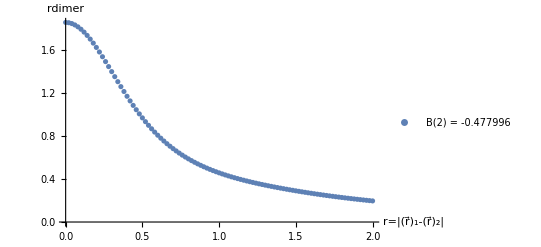

```mathematica
lambdaTest=4;
{eDi,wDi}=ApproxDimerWF[lambdaTest,5,8,20000,0.0001,15,0.05,0];

JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@wDi];
JacobiTrailWavefunctionDataU=Table[JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];

plotData=Transpose[{rR,JacobiTrailWavefunctionDataU}];
ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","rdimer"},PlotLegends->{"B(2) = "<>ToString[eDi]}]
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},(Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Gamma[3/2]/(2 (core[[i]][[2]]+core[[j]][[2]])^(3/2))),{i,Length[core]},{j,Length[core]}]]])^2];

VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta2,eta3,w2,w3},
eta2= (8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Aa((1/4)lam^2 + 2Gg +2  Bb) + (1/4)lam^2Hh +2 Bb Hh+Gg((1/4)lam^2 +2Hh))^(3/2));
w2= 2(1/4)lam^2(Aa+Hh)(Gg+Bb)/((1/4)lam^2 Bb + Aa((1/4)lam^2+2 Gg+2Bb)+(1/4)lam^2 Hh +2 Bb Hh+Gg((1/4)lam^2+2Hh));
eta3 =(8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Gg((1/4)lam^2 + 2Bb)+(1/4)lam^2Hh +2Bb Hh + Aa((1/4)lam^2+2Gg+2Hh))^(3/2));
w3 = 2(1/4)lam^2(Aa+Bb)(Gg+Hh)/((1/4)lam^2 Bb + Gg((1/4)lam^2+2Bb)+(1/4)lam^2 Hh +2Bb Hh+Aa((1/4)lam^2+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2(1/4)lam^2+Bb)+Gg(2(1/4)lam^2 +Bb+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b2=(Gg(4 (1./4) lam^2+2 Bb-2 Hh)+Aa (-4 (1/4) lam^2-2 Bb+2 Hh))/(2 (2 (1/4) lam^2+Aa+Bb+Gg+Hh));
c2=( Gg(2(1/4)lam^2+Bb+Hh)+Aa(2(1/4)lam^2+4Gg+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

a3= (4Bb(2(1/4)lam^2+Hh)+Gg(Bb+2(1/4)lam^2+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4(1/4)lam^2-2Hh)+Aa(4(1/4)lam^2+2Hh-2Bb))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2(1/4)lam^2+Hh)+Aa(4Gg+2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

Sinh1=(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1+100 $MachineEpsilon);
Sinh2=(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2+100 $MachineEpsilon);
Sinh3=(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3+100 $MachineEpsilon);

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

Do[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

(*wmat=ParallelTable[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints},ProgressReporting->False];*) 

AppendTo[Wmats,cij (amat(*+wmat*))];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=(Kmat+Dmat+Wmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
t2=AbsoluteTime[];
(*Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins      |Ψ_d| = ",normsqu];*)
tanDelta
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

R_max = 2.     #(grid points) = 52                a_dd^(1, 2, 3) = 1.93068 , 1.84 , 1.92166 fm

R_max = 3.     #(grid points) = 78                a_dd^(1, 2, 3) = 3.34674 , 3.00168 , 3.31437 fm

R_max = 4.     #(grid points) = 104                a_dd^(1, 2, 3) = 3.28641 , 2.52216 , 3.25186 fm

R_max = 5.     #(grid points) = 130                a_dd^(1, 2, 3) = 3.19393 , 0.44087 , 3.1532 fm

R_max = 6.     #(grid points) = 156                a_dd^(1, 2, 3) = 3.17668 , -2.64329 , 3.13529 fm

R_max = 7.     #(grid points) = 182                a_dd^(1, 2, 3) = 3.17566 , -5.00034 , 3.13424 fm

R_max = 8.     #(grid points) = 208                a_dd^(1, 2, 3) = 3.17564 , -6.03295 , 3.13421 fm

R_max = 9.     #(grid points) = 234                a_dd^(1, 2, 3) = 3.17564 , -6.33777 , 3.13421 fm

R_max = 10.     #(grid points) = 260                a_dd^(1, 2, 3) = 3.17564 , -6.40672 , 3.13421 fm

R_max = 11.     #(grid points) = 286                a_dd^(1, 2, 3) = 3.17564 , -6.41936 , 3.13421 fm

R_max = 12.     #(grid points) = 312                a_dd^(1, 2, 3) = 3.17564 , -6.42127 , 3.13421 fm

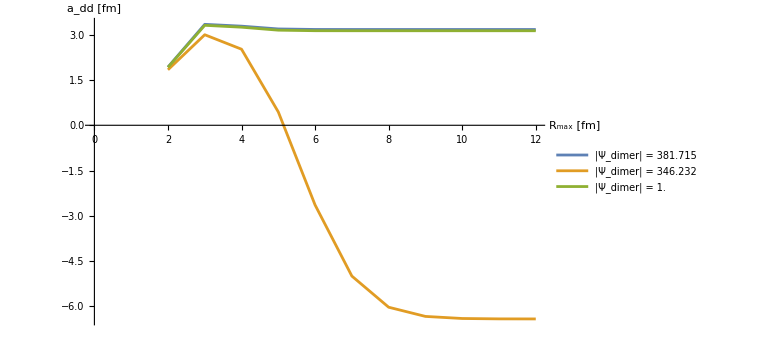
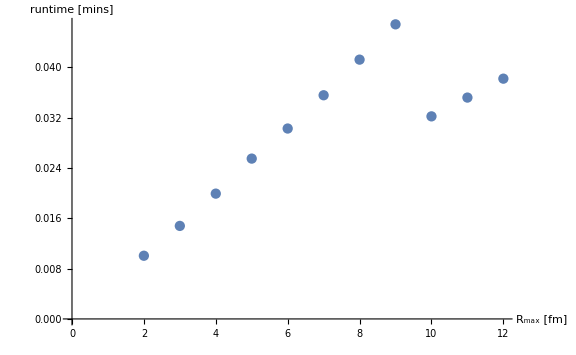
-Graphics- | -Graphics-

```mathematica
lambdaTest=10;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];LECd=0.0;
(* energy at which the scattering length is obtained from the amplitude *)
results={};
{e0Core,dimerCore}={-2.1503854263572664,{{0.8736969096450122,31.968891},{0.4317179845002986,7.071322},{0.20001446920255886,1.649044},{0.09209874781177102,0.388879},{0.0422531028076927,0.07911}}};
{e0Core2,dimerCore2}={-2.283422864385646,{{0.8399054598468957,35.968063},{0.4889102363991713,7.987606},{0.21366543922397682,1.70355},{0.09260119076503445,0.388871},{0.03527261982502021,0.094129},{0.007317178710654077,0.023176}}};
{e0Core3,dimerCore3}={-2.1503854263572664,{{3.86547653406235,31.968891},{1.90999353158479,7.071322},{0.884778427351535,1.649044},{0.407437060085652,0.388879},{0.186519401166625,0.07911}}};
legendEntries="|Ψ_dimer| = "<>ToString[#,TraditionalForm]&/@{1/NormTF[dimerCore],1/NormTF[dimerCore2],1/NormTF[dimerCore3]};
rMaxStart=2.0;
rMaxEnd=12;
nbrR=10;
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
energ=0.001;
grdPerFermi=26;
results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ];
tmp2=GetEREP3[lambdaTest,rMa,nGrd,dimerCore2,LECc,energ];
tmp3=GetEREP3[lambdaTest,rMa,nGrd,dimerCore3,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,{tmp,tmp2,tmp3}];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd^(1, 2, 3) = ",tmp," , ",tmp2," , ",tmp3," fm "];
,{rMa,RmaxRange}]

Grid[{{ListPlot[{Transpose[{RmaxRange,results[[All,1]]}],Transpose[{RmaxRange,results[[All,2]]}],Transpose[{RmaxRange,results[[All,3]]}]},ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"},PlotLegends->legendEntries],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```

```mathematica
NormTFt[core_]:=(Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Gamma[3/2]/(2 (core[[i]][[2]]+core[[j]][[2]])^(3/2))),{i,Length[core]},{j,Length[core]}]]])^2;
```

```mathematica
aa=dimerCore2
num=(NIntegrate[r^2 (Total[#[[1]] Exp[-#[[2]] r^2]&/@aa])^2,{r,0,1000}])^2
ana=NormTFt[aa]
num/ana
```

{{0.839905,35.9681},{0.48891,7.98761},{0.213665,1.70355},{0.0926012,0.388871},{0.0352726,0.094129},{0.00731718,0.023176}}

0.00288824

0.00288824

1.